# Case Study: Maternal Labor Supply and Child Academic Outcomes

## Created by Victor H. Aguiar

## Background

This case study focuses on how a single mother, Lisa, allocates her time between work, child care, and leisure. The objective is to understand how different welfare reform policies might affect both Lisa’s labor supply and her child’s academic outcomes.

## Scenario

Meet Lisa, a single mother in her early 30s, who is contemplating how to allocate her time between work, child care, and leisure as she navigates various welfare reform policies. The time frame of the decision is one week (168 hours).

### Setting up the Problem

c: Consumption goods.

L: Leisure time measured in hours.

m: Time spent on maternal care measured in hours.

l: Time spent on work measured in hours.

T: Total available time, such that l+m+L=T.

p:  Price of consumption goods assumed as constant.

w: Wage rate per hour.

B: Welfare benefits (converted to weekly income)

θ= Academic outcome of the child, given by θ=bm

```mathematica
Clear[f,a,δ,b,p,w,T]
```

```mathematica
f[m_]:=b*m
```

```mathematica
fs=f[m]
```

b m

```mathematica
Dfs=D[f[m],m]
```

b

```mathematica
Clear[L]
```

```mathematica
Lag=c^a+L^a+(f[m])^a+λ*(w*T-p*c-w*(m+L))
```

c^a+L^a+(b m)^a+(-c p-(L+m) w+T w) λ

```mathematica
Lagc=D[Lag,c]
```

a c^(-1+a)-p λ

```mathematica
LagL=D[Lag,L]
```

a L^(-1+a)-w λ

```mathematica
Lagm=D[Lag,m]
```

a b (b m)^(-1+a)-w λ

```mathematica
Lagl=D[Lag,λ]
```

-c p-(L+m) w+T w

## Solving for c,L,s:

```mathematica
λ1=λ/.Solve[Lagc==0,λ][[1]]
```

(a c^(-1+a))/p

```mathematica
λ2=λ/.Solve[LagL==0,λ][[1]]
```

(a L^(-1+a))/w

```mathematica
MRSequation=FullSimplify[λ1/λ2==1]
```

(c^(-1+a) L^(1-a) w)/p==1

```mathematica
Lstep1=FullSimplify[L/.Solve[MRSequation,L][[1]],(1-a)>0&&c>0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

c (p/w)^(1/(1-a))

## Solving for c in terms of s

```mathematica
λ3=λ/.Solve[Lagm==0,λ][[1]]
```

(a (b m)^a)/(m w)

```mathematica
MRS2equation=FullSimplify[λ1/λ3==1]
```

(c^(-1+a) m (b m)^-a w)/p==1

```mathematica
mstep1=FullSimplify[m/.Solve[MRS2equation,m][[1]],(1-a)>0&&c>0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

c ((b^a p)/w)^(1/(1-a))

```mathematica
budgetmodified=FullSimplify[Lagl/.{m->mstep1,L->Lstep1}]
```

T w-c (p+((p/w)^(1/(1-a))+((b^a p)/w)^(1/(1-a))) w)

```mathematica
csol1=FullSimplify[c/.Solve[budgetmodified==0,c][[1]],(1-a)>0&&c>0]
```

(T w)/(p+((p/w)^(1/(1-a))+((b^a p)/w)^(1/(1-a))) w)

```mathematica
Lsol1=FullSimplify[Lstep1/.{c->csol1},(1-a)>0&&c>0]
```

(T (p/w)^(1/(1-a)) w)/(p+((p/w)^(1/(1-a))+((b^a p)/w)^(1/(1-a))) w)

```mathematica
msol1=FullSimplify[mstep1/.{c->csol1,L->Lsol1}]
```

(T w)/(w+((b^a p)/w)^(1/(-1+a)) (p+(p/w)^(1/(1-a)) w))

## Budget check: should give zero

```mathematica
FullSimplify[Lagl/.{c->csol1,L->Lsol1,m->msol1}]
```

0

## Obtain l optimal for working case:

```mathematica
lsol1=l/.Solve[Lsol1+msol1+l==T,l][[1]]
```

(p T)/(p+(p/w)^(1/(1-a)) w+((b^a p)/w)^(1/(1-a)) w)

# Solution with Welfare Benefits B>0

```mathematica
Lag=c^a+L^a+(f[m])^a+λ*(w*T+B-p*c-w*(m+L))
```

c^a+L^a+(b m)^a+(B-c p-(L+m) w+T w) λ

```mathematica
Lagc=D[Lag,c]
```

a c^(-1+a)-p λ

```mathematica
LagL=D[Lag,L]
```

a L^(-1+a)-w λ

```mathematica
Lagm=D[Lag,m]
```

a b (b m)^(-1+a)-w λ

```mathematica
Lagl=D[Lag,λ]
```

B-c p-(L+m) w+T w

## Solving for c,L,s:

```mathematica
λ1=λ/.Solve[Lagc==0,λ][[1]]
```

(a c^(-1+a))/p

```mathematica
λ2=λ/.Solve[LagL==0,λ][[1]]
```

(a L^(-1+a))/w

```mathematica
MRSequation=FullSimplify[λ1/λ2==1]
```

(c^(-1+a) L^(1-a) w)/p==1

```mathematica
Lstep1=FullSimplify[L/.Solve[MRSequation,L][[1]],(1-a)>0&&c>0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

c (p/w)^(1/(1-a))

## Solving for c in terms of s

```mathematica
λ3=λ/.Solve[Lagm==0,λ][[1]]
```

(a (b m)^a)/(m w)

```mathematica
MRS2equation=FullSimplify[λ1/λ3==1]
```

(c^(-1+a) m (b m)^-a w)/p==1

```mathematica
mstep1=FullSimplify[m/.Solve[MRS2equation,m][[1]],(1-a)>0&&c>0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

c ((b^a p)/w)^(1/(1-a))

```mathematica
budgetmodified=FullSimplify[Lagl/.{m->mstep1,L->Lstep1}]
```

B+T w-c (p+((p/w)^(1/(1-a))+((b^a p)/w)^(1/(1-a))) w)

```mathematica
csol1=FullSimplify[c/.Solve[budgetmodified==0,c][[1]],(1-a)>0&&c>0]
```

(B+T w)/(p+((p/w)^(1/(1-a))+((b^a p)/w)^(1/(1-a))) w)

```mathematica
Lsol1=FullSimplify[Lstep1/.{c->csol1},(1-a)>0&&c>0]
```

((p/w)^(1/(1-a)) (B+T w))/(p+((p/w)^(1/(1-a))+((b^a p)/w)^(1/(1-a))) w)

```mathematica
msol1=FullSimplify[mstep1/.{c->csol1,L->Lsol1}]
```

(B+T w)/(w+((b^a p)/w)^(1/(-1+a)) (p+(p/w)^(1/(1-a)) w))

## Budget check: should give zero

```mathematica
FullSimplify[Lagl/.{c->csol1,L->Lsol1,m->msol1}]
```

0

## Obtain l optimal for working case:

```mathematica
lsol1=FullSimplify[l/.Solve[Lsol1+msol1+l==T,l][[1]],(1-a)>0&&c>0]
```

(-B+(p (B+T w))/(p+((p/w)^(1/(1-a))+((b^a p)/w)^(1/(1-a))) w))/w

```mathematica
thetasol1=f[msol1]
```

(b (B+T w))/(w+((b^a p)/w)^(1/(-1+a)) (p+(p/w)^(1/(1-a)) w))

```mathematica
w=1
```

1

```mathematica
T=168
```

168

```mathematica
a=1/2
```

1/2

```mathematica
p=1
```

1

```mathematica
b=1/2
```

1/2

```mathematica
lsol1
```

-B+(2 (168+B))/5

```mathematica
thetasol1
```

(168+B)/10

```mathematica
Clear[δ]
```

```mathematica
Z=lsol1^δ*(thetasol1)^(1-δ)
```

10^(-1+δ) (168+B)^(1-δ) (-B+(2 (168+B))/5)^δ

```mathematica
DerZ=D[Z,B]
```

10^(-1+δ) (168+B)^-δ (-B+(2 (168+B))/5)^δ (1-δ)-3 2^(-1+δ) 5^(-2+δ) (168+B)^(1-δ) (-B+(2 (168+B))/5)^(-1+δ) δ

```mathematica
δ=1/3
```

1/3

```mathematica
FullSimplify[DerZ]
```

(56-3 B)/(5 (672-6 B)^(2/3) (168+B)^(1/3))

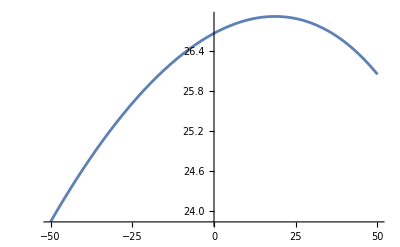

```mathematica
Plot[Z,{B,-50,50}]
```

```mathematica
DerZ
```

-(168+B)^(2/3)/(5 10^(2/3) (-B+(2 (168+B))/5)^(2/3))+(2^(1/3) (-B+(2 (168+B))/5)^(1/3))/(3 5^(2/3) (168+B)^(1/3))

```mathematica
Reduce[DerZ==0,B]
```

B==56/3

```mathematica
Diff=FullSimplify[csol/csol2,a>0&&a<1&&b>0&&(R<w*lsol)]
```

(48 √(3/5))/(5 R)

```mathematica
FullSimplify[Reduce[{Diff<=1,R<=w*lsol},R]]
```

R<0||(48 √(3/5))/5≤R≤48/5

```mathematica
N[FullSimplify[Reduce[{Diff<=1,R<=w*lsol},R]]]
```

R<0.||7.43613≤R≤9.6